```mathematica
PacletDirectoryAdd["~/github/EcoEvo"];
```

PacletDirectoryAdd::expobs: The experimental function PacletDirectoryAdd is now obsolete and is superseded by PacletDirectoryLoad.

```mathematica
<<EcoEvo`
```

EcoEvo Package Version 1.5.3X (November 14, 2020)
Christopher A. Klausmeier <christopher.klausmeier@gmail.com>

The option you're looking for is BoundaryDetection (False by default), which is implemented for FindEcoEq, FindEcoEvoEq, EcoEvoSim and FindEvoEq.  It puts a hard border on the edge of trait-space.

```mathematica
?BoundaryDetection
```

Standard LV comp example, with narrow range for x:

```mathematica
SetModel[{
Guild[n]->{Equation->g,Trait[x]->{Range->Interval[{-0.25,0.25}]}}
}]
g[i_]:=(1-Sum[a[Subscript[x, i],Subscript[x, j]]*Subscript[n, j][t],{j,Subscript[𝒩, n]}]/k[Subscript[x, i]])*Subscript[n, i][t];
a[xi_,xj_]:=E^(-1/2*(xi-xj)^2/σ^2);
k[x_]:=1-x^2;
σ=0.6;
```

EcoEvoSim (BoundaryDetection->False):

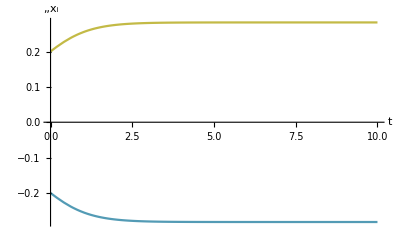

{n_1→0.560349,n_2→0.560349,x_1→-0.282213,x_2→0.282213}

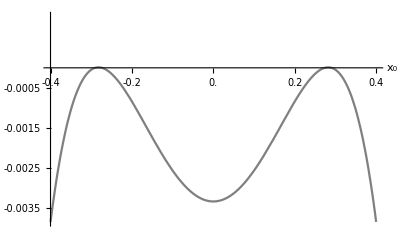

```mathematica
sol=EcoEvoSim[{Subscript[x, 1]->-0.2,Subscript[x, 2]->0.2,Subscript[n, 1]->0.5,Subscript[n, 2]->0.5},10];
PlotDynamics[sol,x]
FinalSlice[sol]
PlotInv[FinalSlice[sol],{Subscript[x, 0],-0.4,0.4}]
```

BoundaryDetection->True:

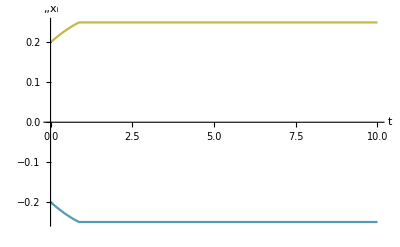

{n_1→0.549319,n_2→0.549319,x_1→-0.25,x_2→0.25}

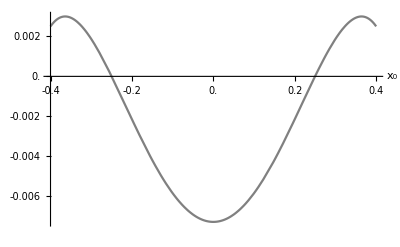

```mathematica
sol=EcoEvoSim[{Subscript[x, 1]->-0.2,Subscript[x, 2]->0.2,Subscript[n, 1]->0.5,Subscript[n, 2]->0.5},10,BoundaryDetection->True];
PlotDynamics[sol,x]
FinalSlice[sol]
PlotInv[FinalSlice[sol],{Subscript[x, 0],-0.4,0.4}]
```

I thought something like this might also work, but evidently not.  If you need it, I could probably make it happen.

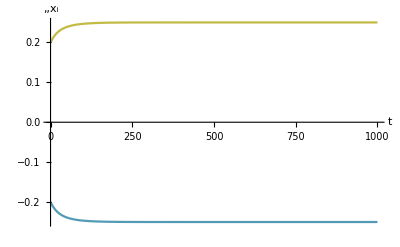

{n_1→0.549322,n_2→0.549322,x_1→-0.25,x_2→0.25}

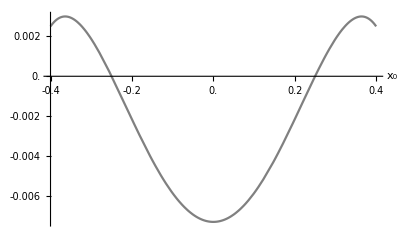

```mathematica
sol=EcoEvoSim[{Subscript[x, 1]->-0.2,Subscript[x, 2]->0.2,Subscript[n, 1]->0.5,Subscript[n, 2]->0.5},{V[x]->-(x+0.25)(x-0.25)},10^3];
PlotDynamics[sol,x]
FinalSlice[sol]
PlotInv[FinalSlice[sol],{Subscript[x, 0],-0.4,0.4}]
```

```mathematica
`
```

FindEcoEvoEq, BoundaryDetection->False:

```mathematica
FindEcoEvoEq[{Subscript[x, 1]->-0.2,Subscript[x, 2]->0.2,Subscript[n, 1]->0.5,Subscript[n, 2]->0.5}]
```

{n_1→0.560356,n_2→0.560356,x_1→-0.282213,x_2→0.282213}

FindEcoEvoEq, BoundaryDetection->True:

```mathematica
FindEcoEvoEq[{Subscript[x, 1]->-0.2,Subscript[x, 2]->0.2,Subscript[n, 1]->0.5,Subscript[n, 2]->0.5},BoundaryDetection->True]
```

FindRoot::reged: The point {0.522236,0.522236,-0.25,0.25} is at the edge of the search region {-0.25,0.25} in coordinate 4 and the computed search direction points outside the region.

FindEcoEvoEq::reged: Warning: FindRoot reached boundary, don't trust result (maybe try again using Fixed to fix variables on the boundary).

{n_1→0.522236,n_2→0.522236,x_1→-0.25,x_2→0.25}

Note that this final result is just where FindRoot quit -- not the right answer!  For that, you could use Fixed or FindEcoEq:

```mathematica
FindEcoEvoEq[{Subscript[x, 1]->-0.2,Subscript[x, 2]->0.2,Subscript[n, 1]->0.5,Subscript[n, 2]->0.5},Fixed->{Subscript[x, 1]->-0.25,Subscript[x, 2]->0.25}]
```

{n_1→0.549322,n_2→0.549322,x_1→-0.25,x_2→0.25}

```mathematica
FindEcoEq[{Subscript[x, 1]->-0.25,Subscript[x, 2]->0.25,Subscript[n, 1]->0.5,Subscript[n, 2]->0.5}]
```

{n_1→0.549322,n_2→0.549322}

A different error if you START out of bounds:

```mathematica
FindEcoEvoEq[{Subscript[x, 1]->-0.3,Subscript[x, 2]->0.3,Subscript[n, 1]->0.5,Subscript[n, 2]->0.5},BoundaryDetection->True]
```

FindEcoEvoEq::streg: Initial value of x_1 = -0.3 is outside the range -0.25 < x_1 < 0.25. Either fix it or set BoundaryDetection→False.

$Aborted

One other thing that I thought would work, but doesn't.  Maybe I'll fix this later:

```mathematica
FindEcoEvoEq[{Subscript[n, 1]->0.5,Subscript[n, 2]->0.5},Fixed->{Subscript[x, 1]->-0.25,Subscript[x, 2]->0.25}]
```

FindEcoEvoEq[{n_1→0.5,n_2→0.5},Fixed→{x_1→-0.25,x_2→0.25}]